```mathematica
λ=1.35*I+3.9;
soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z]
z1=z/.soluciones[[1]]
z2=z/.soluciones[[2]]
z3=z/.soluciones[[3]]
```

{{z→0.279922+2.0705 ⅈ},{z→1.03151-2.88673 ⅈ},{z→1.15942+0.217111 ⅈ}}

0.279922+2.0705 ⅈ

1.03151-2.88673 ⅈ

1.15942+0.217111 ⅈ

```mathematica
p[z_]:=(z^2-1)(z-λ);lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z];
iterSch= Compile[{{z,_Complex}},sp[z]];
r1=1;r2=-1;r3=λ;
Clear[rootPosition]
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
colorLevelWS= Compile[{{p,_Real}},0.4*FractionalPart[p]];
fractalColorWS[p_] :=
Block[{pp = colorLevelWS[p]},
Switch[IntegerPart[p],
3, CMYKColor[0.6+pp,0.,0.,2*pp],
2, CMYKColor[0.,0.6+pp,0.,2*pp],
1, CMYKColor[0.,0.,0.6+pp,2*pp],
0, CMYKColor[0.,0.,0.,1.]
]
]
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,4},(* Three roots *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

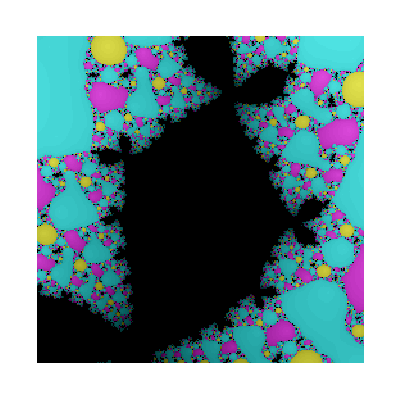

```mathematica
numberPoints =254;
limIterations=50;
xxMin=Re[z2]-1; xxMax=Re[z2]+1; yyMin=Im[z2]-1; yyMax=Im[z2]+1;
plotColorFractal[iterSch, numberPoints]
```

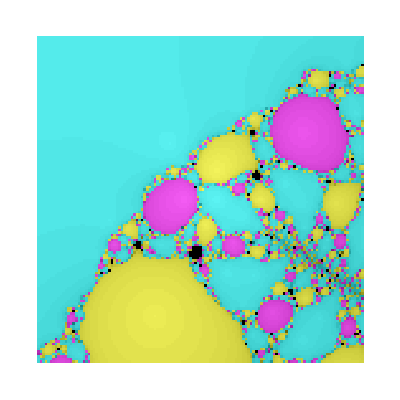

```mathematica
numberPoints =128;
limIterations=50;
xxMin=-10; xxMax=10; yyMin=-10; yyMax=10;
plotColorFractal[iterSch, numberPoints]
```

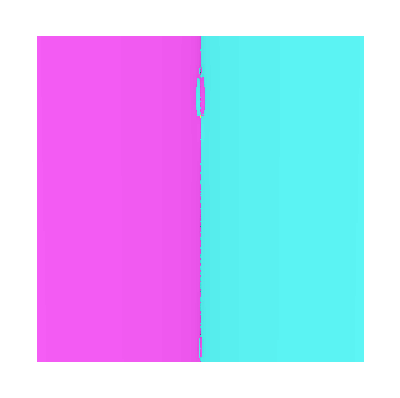

```mathematica
numberPoints =256;
limIterations=100;
xxMin=-0.25; xxMax=0.25; yyMin=0.25; yyMax=0.32;
plotColorFractal[iterSch, numberPoints]
```

```mathematica
NestList[sp,z1,100]
```

{0.279922+2.0705 ⅈ,-0.708092-2.84301 ⅈ,-0.0950052+1.30886 ⅈ,-3.52899-4.88494 ⅈ,0.327711+0.749354 ⅈ,2.07623+0.687873 ⅈ,1.50765+0.465889 ⅈ,1.02493+0.077969 ⅈ,1.00136-0.000251142 ⅈ,1.-9.00424×10^-8 ⅈ,1.-4.78333×10^-14 ⅈ,1.-6.18467×10^-28 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

```mathematica
NestList[sp,z2,100]
```

{1.03151-2.88673 ⅈ,0.227775+1.48928 ⅈ,-0.0331028-3.71511 ⅈ,0.190952+1.3266 ⅈ,0.888825-4.82407 ⅈ,0.41928+1.35403 ⅈ,0.983921-2.83857 ⅈ,0.228087+1.48994 ⅈ,-0.0345865-3.71139 ⅈ,0.190231+1.32679 ⅈ,0.881723-4.83093 ⅈ,0.419572+1.35258 ⅈ,0.991928-2.83516 ⅈ,0.228205+1.48979 ⅈ,-0.0335686-3.71144 ⅈ,0.190351+1.32693 ⅈ,0.88089-4.82856 ⅈ,0.419206+1.35267 ⅈ,0.991869-2.83738 ⅈ,0.228161+1.48978 ⅈ,-0.0336967-3.71166 ⅈ,0.190369+1.32689 ⅈ,0.881506-4.82865 ⅈ,0.419267+1.35274 ⅈ,0.99139-2.83711 ⅈ,0.228164+1.4898 ⅈ,-0.0337298-3.71161 ⅈ,0.190358+1.32689 ⅈ,0.881417-4.82877 ⅈ,0.419275+1.35272 ⅈ,0.991502-2.83704 ⅈ,0.228166+1.48979 ⅈ,-0.0337147-3.71161 ⅈ,0.190359+1.32689 ⅈ,0.8814-4.82874 ⅈ,0.41927+1.35272 ⅈ,0.991506-2.83707 ⅈ,0.228165+1.48979 ⅈ,-0.033716-3.71161 ⅈ,0.19036+1.32689 ⅈ,0.881409-4.82874 ⅈ,0.41927+1.35272 ⅈ,0.991498-2.83707 ⅈ,0.228165+1.48979 ⅈ,-0.0337167-3.71161 ⅈ,0.190359+1.32689 ⅈ,0.881408-4.82874 ⅈ,0.41927+1.35272 ⅈ,0.991499-2.83707 ⅈ,0.228165+1.48979 ⅈ,-0.0337164-3.71161 ⅈ,0.190359+1.32689 ⅈ,0.881408-4.82874 ⅈ,0.41927+1.35272 ⅈ,0.9915-2.83707 ⅈ,0.228165+1.48979 ⅈ,-0.0337164-3.71161 ⅈ,0.190359+1.32689 ⅈ,0.881408-4.82874 ⅈ,0.41927+1.35272 ⅈ,0.991499-2.83707 ⅈ,0.228165+1.48979 ⅈ,-0.0337165-3.71161 ⅈ,0.190359+1.32689 ⅈ,0.881408-4.82874 ⅈ,0.41927+1.35272 ⅈ,0.991499-2.83707 ⅈ,0.228165+1.48979 ⅈ,-0.0337165-3.71161 ⅈ,0.190359+1.32689 ⅈ,0.881408-4.82874 ⅈ,0.41927+1.35272 ⅈ,0.991499-2.83707 ⅈ,0.228165+1.48979 ⅈ,-0.0337165-3.71161 ⅈ,0.190359+1.32689 ⅈ,0.881408-4.82874 ⅈ,0.41927+1.35272 ⅈ,0.991499-2.83707 ⅈ,0.228165+1.48979 ⅈ,-0.0337165-3.71161 ⅈ,0.190359+1.32689 ⅈ,0.881408-4.82874 ⅈ,0.41927+1.35272 ⅈ,0.991499-2.83707 ⅈ,0.228165+1.48979 ⅈ,-0.0337165-3.71161 ⅈ,0.190359+1.32689 ⅈ,0.881408-4.82874 ⅈ,0.41927+1.35272 ⅈ,0.991499-2.83707 ⅈ,0.228165+1.48979 ⅈ,-0.0337165-3.71161 ⅈ,0.190359+1.32689 ⅈ,0.881408-4.82874 ⅈ,0.41927+1.35272 ⅈ,0.991499-2.83707 ⅈ,0.228165+1.48979 ⅈ,-0.0337165-3.71161 ⅈ,0.190359+1.32689 ⅈ,0.881408-4.82874 ⅈ}

```mathematica
NestList[sp,z3,100]
```

{1.15942+0.217111 ⅈ,1.00425-0.00436278 ⅈ,0.999995+8.08613×10^-6 ⅈ,1.+2.23916×10^-11 ⅈ,1.+7.62299×10^-23 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}